### Critically Damped Values: L=C, R=0.5; Underdamped Values= R = 500k, C = 6uF, L = 9nH; Overdamped Values = R = 0.3, C = L = 1;

ζ= 1.66667 > 1 → overdamped

V_c(t) = 3. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))

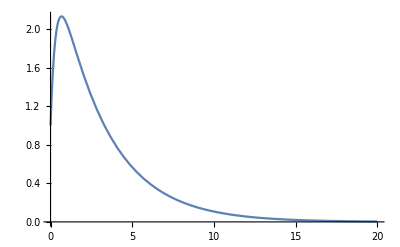

iL(t) = 0.666667 ⅇ^(-3. t)-9. ⅇ^(-0.333333 t)

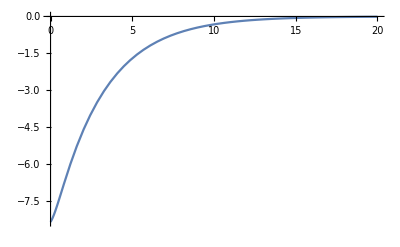

```mathematica
(*This Program gets the natural response of a simple parallel RLC circuit with no external source*)
Clear["Global`*"]
R = 0.3(*Input["Enter The Value Of Resistance"]*);
Capacitor=1(*Input["Enter The Value Of Capacitance"]*);
L= 1(*Input["Enter The Value Of L"]*);
ωc=√(1/(L Capacitor));
ζ = 1/(2 ωc R Capacitor);
eqn1=V''[t]+2 ζ ωc V'[t]+ωc^2 V[t]==0;
capVoltage = DSolve[{eqn1, V[0]==1, V'[0]==5},V[t],t][[1]];
Vc[t_]:=V[t]/.capVoltage
inductorCurrent=1/L∫Vc[t]ⅆt;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,18]
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]

Plot[Vc[t],{t,0,20}, PlotRange->Automatic]
i[t_]:=inductorCurrent;
Style[StringForm["iL(t) = ``",i[t]], Blue, 18]
Plot[i[t],{t,0,20}]
```

```mathematica
ClearAll[R,L,Capacitor,ωc,ζ]
```

```mathematica
(*This Program outputs the natural response of a series RLC circuit*)
```

```mathematica
R = 500000(*Input["Enter The Value Of Resistance"]*);
Capacitor=0.000006(*Input["Enter The Value Of Capacitance"]*);
L= 0.000000009(*Input["Enter The Value Of L"]*);
```